```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
<<IGraphM`
Off[Power::infy]
Off[Infinity::indet]
```

```mathematica
adj[α_,λ_,n_]:=Module[{prob0,adj0},
prob0=Table[α λ^(Abs[i-j]-1),{i,n},{j,n}];
prob0=prob0-DiagonalMatrix[Diagonal[prob0]];
adj0=RandomReal[{0,1},{n,n}];
adj0=adj0-DiagonalMatrix[Diagonal[adj0]];
Boole[Table[adj0[[i,j]]<prob0[[i,j]],{i,n},{j,n}]]
]
```

```mathematica
AdjacencyGraph[adj[0.5,0.5,10]]
```

-Graphics-

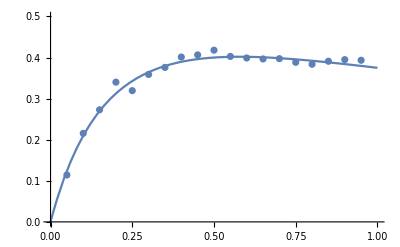

```mathematica
GCC=Table[GlobalClusteringCoefficient[AdjacencyGraph[adj[1,i,500]]],{i,0.05,1,0.05}];
Show[Plot[(3 λ)/((1+λ)(1+3 λ)),{λ,0,1},PlotRange->{0,0.5}],
ListPlot[Transpose[{Table[i,{i,0.05,1,0.05}],GCC}],PlotRange->{0,0.5}]]
```

```mathematica
prob1[α_,λ_,n_]:=Table[α λ^(Abs[i-j]-1),{i,n},{j,n}];
pr=prob1[0.5,0.5,5];
pr-DiagonalMatrix[Diagonal[pr]]//MatrixForm
```

(0. | 0.5 | 0.25 | 0.125 | 0.0625
0.5 | 0. | 0.5 | 0.25 | 0.125
0.25 | 0.5 | 0. | 0.5 | 0.25
0.125 | 0.25 | 0.5 | 0. | 0.5
0.0625 | 0.125 | 0.25 | 0.5 | 0.)

```mathematica
Simplify[Limit[Product[(1-lambda^(-k))^2,k],k->Infinity]]
```

lim_(k→∞) QPochhammer[1/lambda,1/lambda,-1+k]^2